```mathematica
Zdol=((r2+s*L)^-1+s*c )^-1
```

1/(1/(1.62+0.01968 s)+2.2×10^-6 s)

```mathematica
k=FullSimplify[Zdol/(Zdol+R)]
```

(24139.9+293.255 s)/(2.3121×10^7+s (375.572+1. s))

```mathematica
impulseresponse=TrigReduce[Simplify[InverseLaplaceTransform[k, s, t]]]
```

ⅇ^((-187.786-4804.76 ⅈ) t) ((146.628-3.21862 ⅈ)+(146.628+3.21862 ⅈ) ⅇ^((0.+9609.52 ⅈ) t))

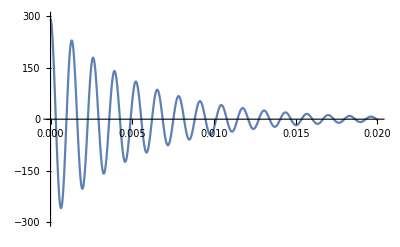

```mathematica
Plot[impulseresponse,{t, 0, 0.02}, PlotRange->{-300,300}]
```

```mathematica
stepresponse=TrigReduce[Simplify[InverseLaplaceTransform[k/s, s, t]]]
```

0.00104407-(0.000522035-0.0304968 ⅈ) ⅇ^((-187.786-4804.76 ⅈ) t)-(0.000522035+0.0304968 ⅈ) ⅇ^((-187.786+4804.76 ⅈ) t)

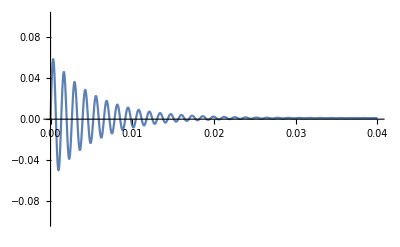

```mathematica
Plot[stepresponse,{t, 0,0.04}, PlotRange->{-0.1,0.1}]
```

```mathematica
R=1550
```

1550

```mathematica
r2=1.62
```

1.62

```mathematica
c=2.2*10^-6
```

2.2×10^-6

```mathematica
L=19.68*10^-3
```

0.01968